```mathematica
(* This notebook analyzes the dynamics of NNC and BBC estimates of the FPR of the RF monitor, as well as their errors (MSE, RMSE), depending on the amount of the data provided to both analyses for estimation. NCC gets atomic pipeline detector traces as data; BBC gets RF monitor traces as data. *) 

NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"file-ops.nb"]]];
```

```mathematica
(*** NCC ESTIMATES ***)
Clear[predRfMonFPRTheor];

(* final NCC formula *) 
predRfMonFPRTheor[detFNR_, dInProp_, pDetNCH0_:0(* for this context *)] := 1 -(1 - detFNR + pDetNCH0)^(dInProp+1);
```

```mathematica
(*** ANALYSIS ***)
```

```mathematica
Clear[getRfFPRPointEstsWithMonH0ct, getRfFNRPointEstResidualsWithH0ct, getRfFprMSQPairsWithBins];

(* provides a list of triples: (monH0InfoCt, our RF mon FPR est, data RF mon FPR est) *) 
getRfFPRPointEstsWithMonH0ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predRfMonFPRTheor[predFNRfromData[#, detFilenames], winSize], predFPRfromData[#, monFilenames, winSize,(*mon num*)11]}&/@ sampleAcrossAllStatelessSubsets[seshNums, sampleCtPerSubset]), "h0count",monFilenames, winSize, 11];


(* provides a list of absolute residuals for above: (h1InfoCt, abs residual for our mon FNR est, abs residual for data mon FNR est) *) 
getRfFNRPointEstResidualsWithH0ct[seshNums_, sampleCtPerSubset_, winSize_] := With[{gtValue=predRfMonFPRTheor[0.1, winSize]},({#[[1]], Abs[#[[2]]-gtValue],Abs[#[[3]]-gtValue]  } & /@ getRfFPRPointEstsWithMonH0ct[seshNums, sampleCtPerSubset, winSize])];

(* provides a list of (bin start, bin elem count, mean squared error for our appr, mean squared error for data appr) ; bin end determined by bin size *) 
getRfFprMSQPairsWithBins[seshNums_, sampleCtPerSubset_, winSize_, binSize_]:= With[{h1CtTwoEstList= (*a list of triples (h0ct, our fpr est, data fpr est *) getRfFNRPointEstResidualsWithH0ct[seshNums, sampleCtPerSubset, winSize] },
(* convert h1cts into bin starts *) Flatten[#]&/@Transpose[{(Range[0,  Max@h1CtTwoEstList[[All,1]], binSize]),({Length@#, Mean@(#[[All,2]]^2), Mean@(#[[All,3]]^2)} &/@ binListsBy[h1CtTwoEstList, {First, 0, Max@h1CtTwoEstList[[All,1]]+binSize-1, binSize}])}]];
```

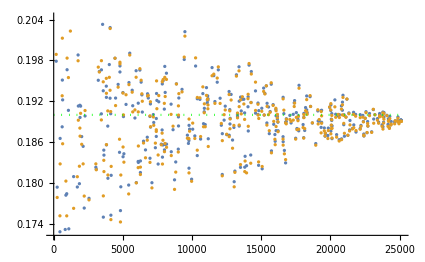
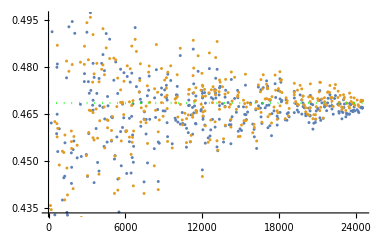
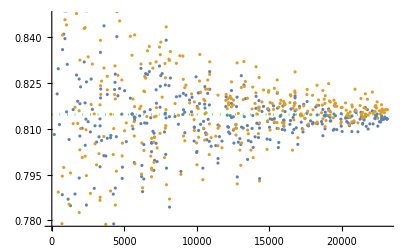
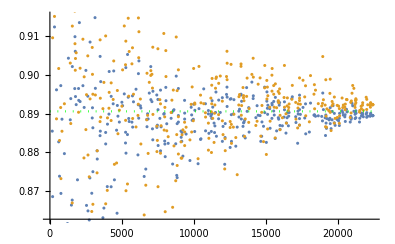
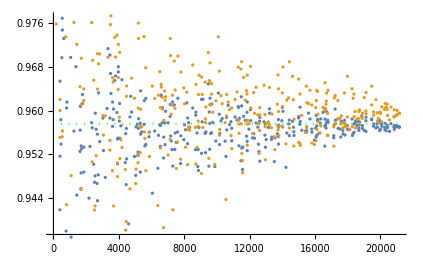
```mathematica
(** FIXED CONVERGENCE CHARTS **) 
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, #]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, #], Max@data[[All,1]]]]] & /@ {1, 5, 10, 15, 20, 29} 
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

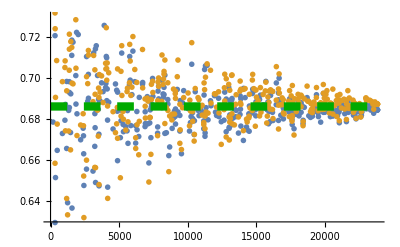

```mathematica
(** PRODUCTION READY ESTIMATE CHARTS **)
plotRfFpr= With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.63,0.73}, PlotMarkers->{"OpenMarkers", Large}], chartHorLine[predRfMonFPRTheor[0.1, 10], Max@data[[All,1]],0, Darker@Green, {AbsoluteThickness[6],AbsoluteDashing[12]}]]]
```

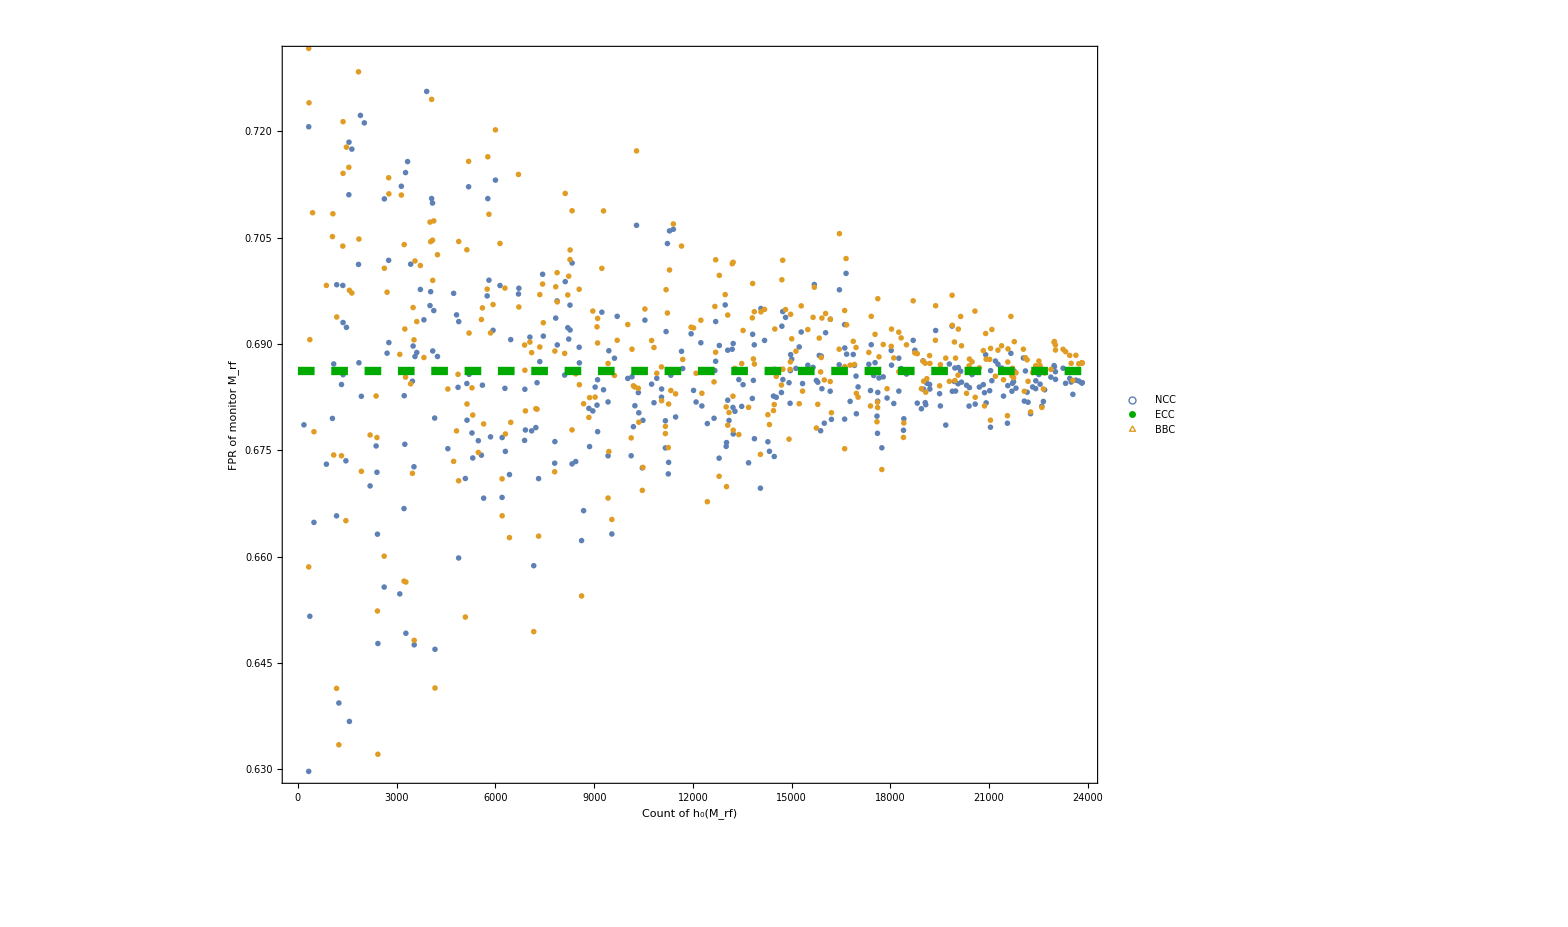

```mathematica
(* no CI line *)
plotRfFprLegended = Legended[Show[plotRfFpr, Frame->True, FrameLabel->{StringJoin["Count of ", ToString[ Style[StringJoin[ToString[Subscript[ "h", "0"],StandardForm], "(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FPR of monitor ", ToString[Style[Subscript[ "M", "rf"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},{AbsoluteDashing[6],AbsoluteThickness[4],Darker@Green} , {ColorData[97,"ColorList"][[2]]}},{"NCC","ECC", "BBC"},
LegendMarkerSize->20,LegendMarkers->{Style[○,Bold,FontSize->28] , Graphics[{Line[{{-10,0},{10,0}}]}],Style[△,Bold,FontSize->28] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

```mathematica
rfDataForNow = getRfFPRPointEstsWithMonH0ct[{4,5,6,7},(*samples per subset*)5, (*winsize*)10];
```

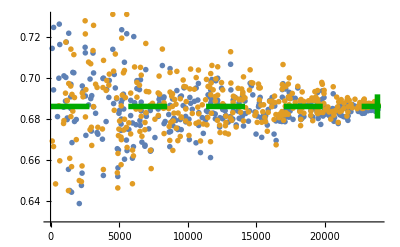

```mathematica
(* PRODUCTION READY EST CHART (with ci line) *)
plotRfFprWithCi= With[{data=rfDataForNow},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.63,0.73}, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}], chartHorLine[predRfMonFPRTheor[0.1, (*winsize*)10], Max@data[[All,1]],0, Darker@Green, {Thickness[0.01],AbsoluteDashing[28]}],ListPlot[{{Max@data[[All,1]],interWald[Max@data[[All,1]]*predRfMonFPRTheor[0.1, (*winsize*)10], Max@data[[All,1]], 0.95] }}, PlotStyle->{Darker@Green,Thickness[0.01]}]]]
```

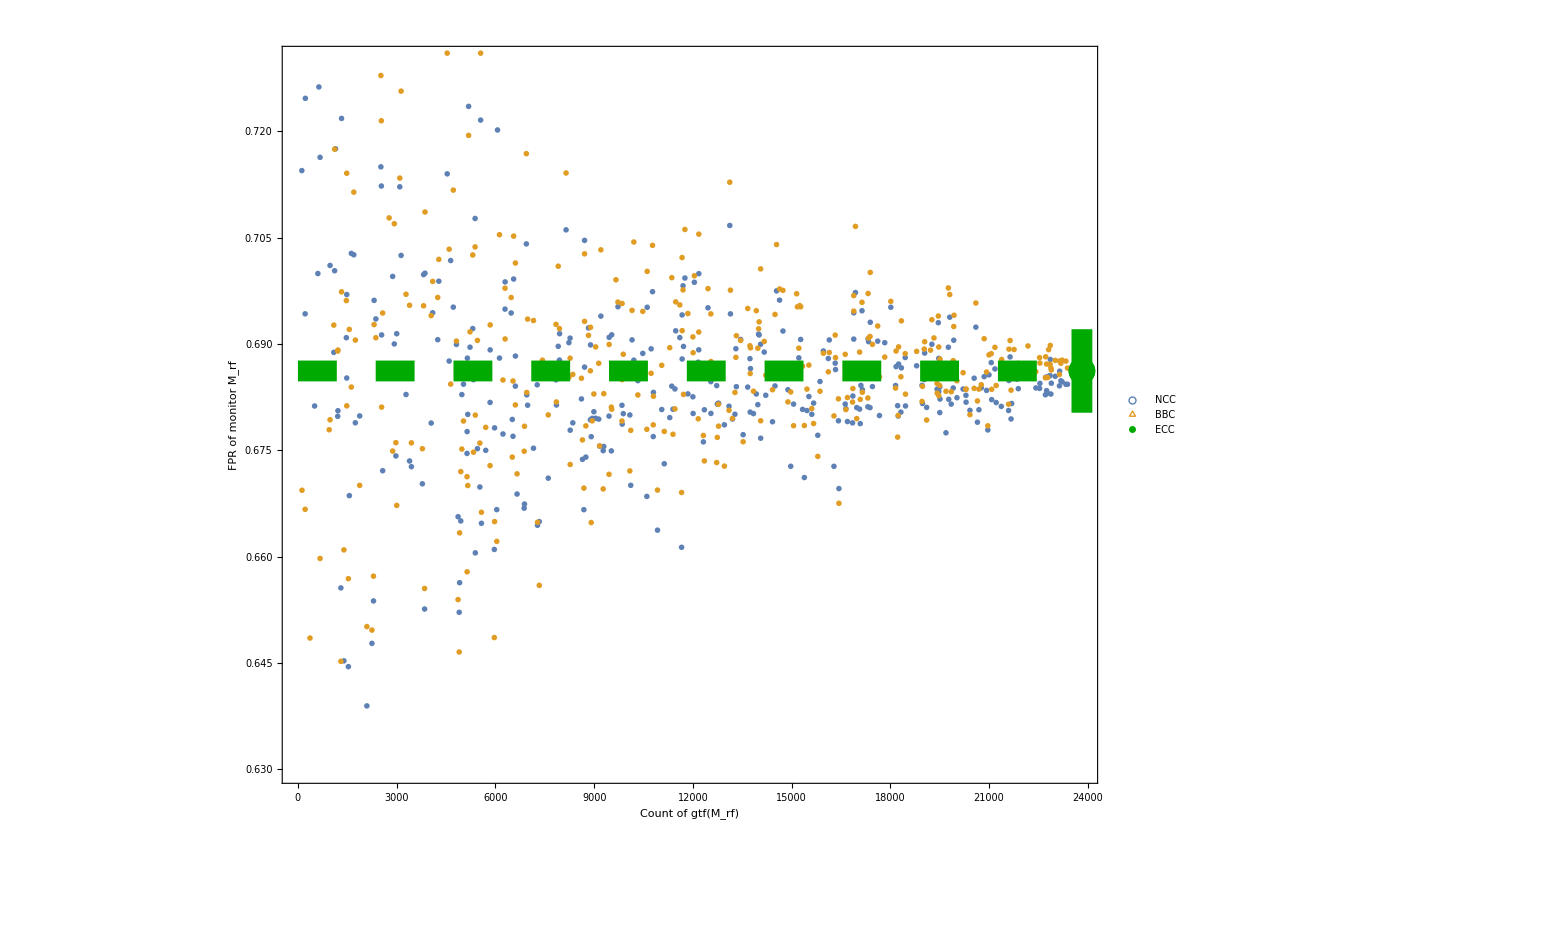

```mathematica
(* with CI line and legend *)
plotRfFprLegended = Legended[Show[plotRfFprWithCi, Frame->True, FrameLabel->{StringJoin["Count of gtf", ToString[ Style[StringJoin[ "(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FPR of monitor ", ToString[Style[Subscript[ "M", "rf"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->45}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},  {ColorData[97,"ColorList"][[2]]},{AbsoluteDashing[10],AbsoluteThickness[6],Darker@Green}},{"NCC","BBC","ECC" },
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] ,Style[△,Bold,FontSize->60], Graphics[{Line[{{-10,0},{10,0}}]}](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

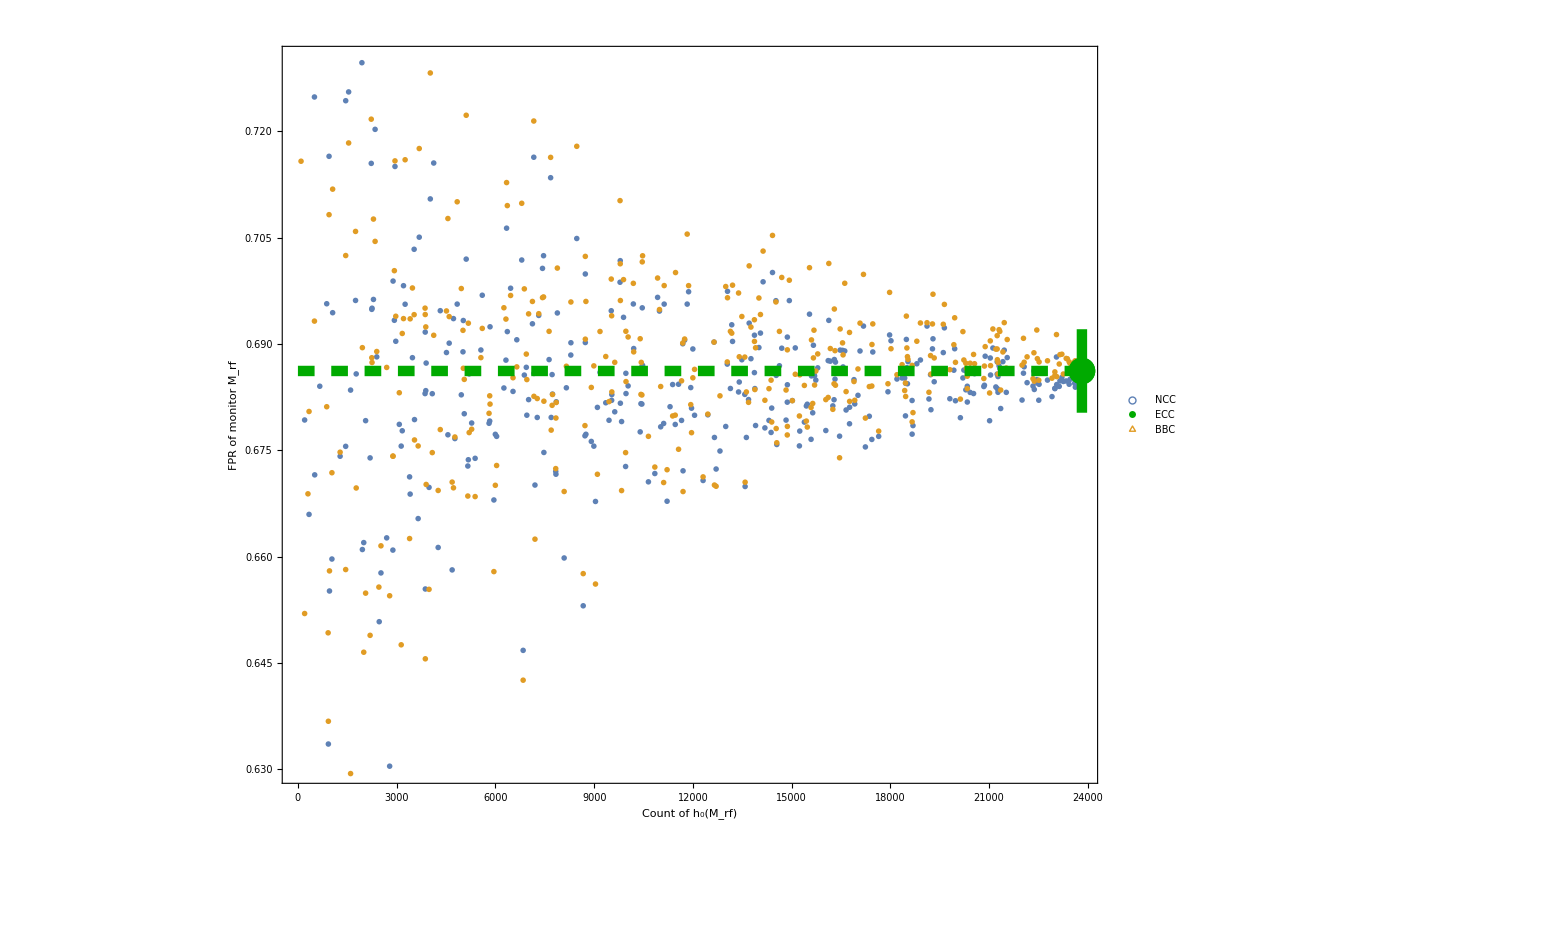

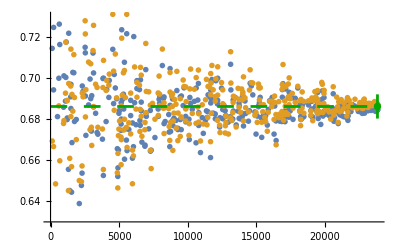

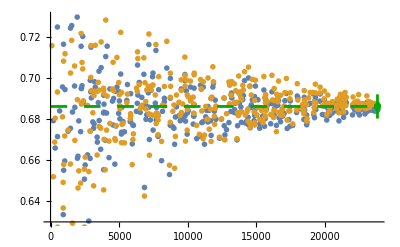

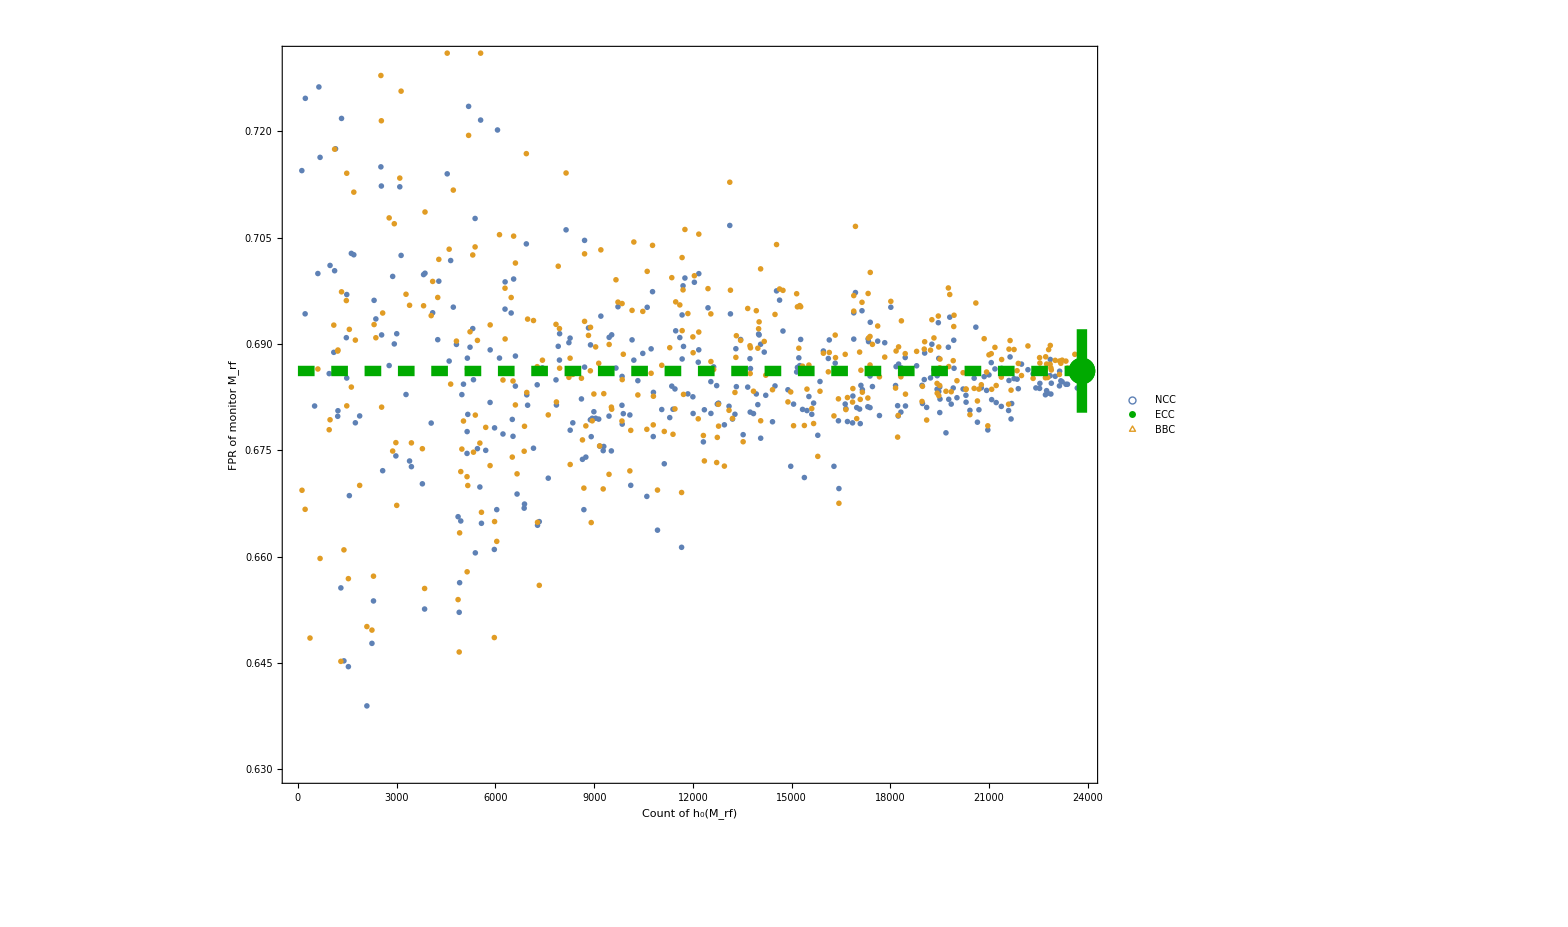

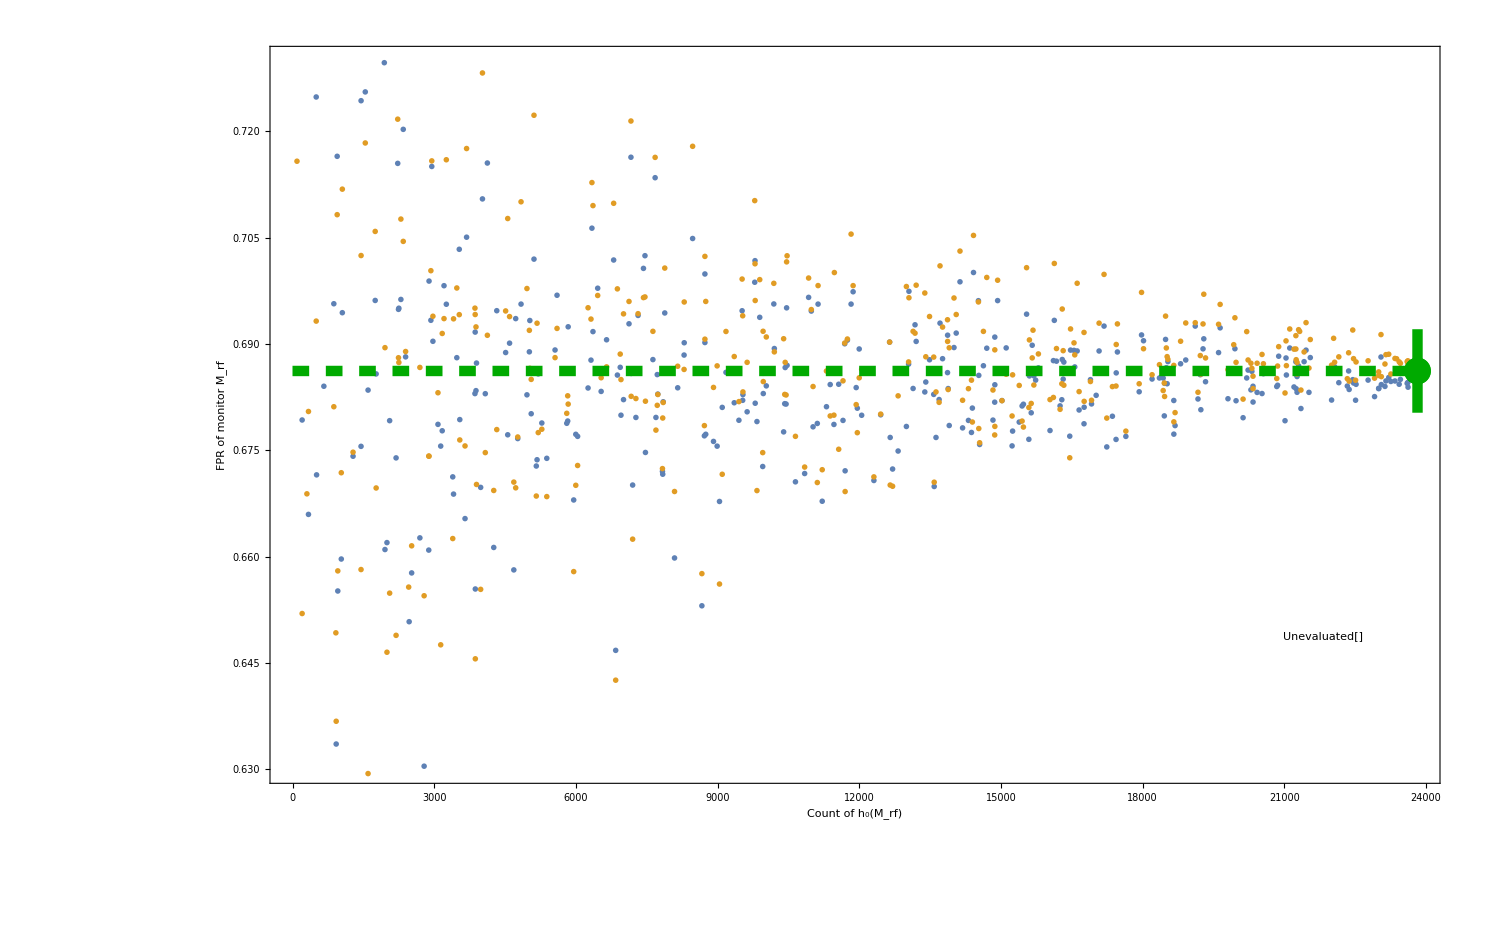

```mathematica
(*** CHARTS OF MSE AND RMSE DYNAMICS IN RESPONSE TO DATA QUANTITY ***)
```

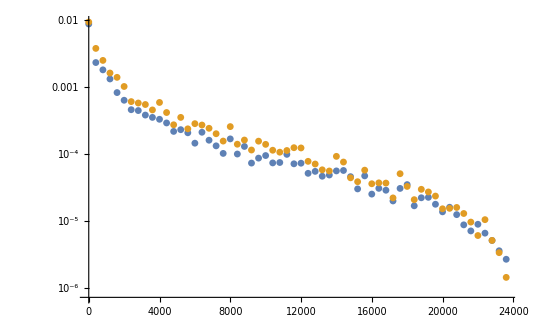

```mathematica
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)400];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[10,10]
```

```mathematica
(* values, for the record *) 
data
```

```mathematica
mseRfdata= {{0,39,0.008753846063883951,0.009364130868615232},{400,43,0.002327274909250556,0.003786250647802682},{800,49,0.0018102315750221408,0.0025044283445789742},{1200,48,0.0013232966854286648,0.0016233764352973608},{1600,53,0.0008286104012448295,0.0013990184748609985},{2000,49,0.000636400610136973,0.001021699538341888},{2400,49,0.0004598834766204994,0.0006073842638642064},{2800,42,0.00044643159226292805,0.0005787157232414234},{3200,51,0.0003823659224167602,0.0005496409905057145},{3600,58,0.00035303471207587543,0.00045612877513680124},{4000,40,0.00033070940383937643,0.0005899910107008688},{4400,58,0.0002915924575237467,0.00041727653703346664},{4800,46,0.000218038282491525,0.0002736945155611596},{5200,47,0.00023137501087496957,0.00035296655448824446},{5600,45,0.00020798033813996446,0.00023814800189202203},{6000,60,0.00014539473507203414,0.00028442503550484677},{6400,36,0.00021179527179475576,0.0002714024345678539},{6800,51,0.00016101680389904221,0.00024271709491385503},{7200,38,0.0001327039152203665,0.00020125753425706162},{7600,59,0.0001023142760984767,0.00015633966952831774},{8000,49,0.00016854932695272964,0.0002571014489224543},{8400,54,0.00010017880036309966,0.0001403612019730609},{8800,43,0.0001300087452955154,0.00016203718493481133},{9200,42,0.00007336047055548691,0.00011497683922188153},{9600,47,0.00008699110782089908,0.0001558677770603709},{10000,47,0.00009504322457307208,0.00013966277560495275},{10400,58,0.00007380197600094737,0.00011408920660112812},{10800,50,0.00007482319446145787,0.00010669451812461147},{11200,49,0.00009905905834334047,0.00011301978240244829},{11600,48,0.00007155925895277674,0.00012449271462340993},{12000,49,0.00007306117476867106,0.00012347408499420535},{12400,45,0.000051582207120326154,0.00007789011068375261},{12800,52,0.00005518841966850562,0.00007106254062743468},{13200,42,0.00004669488301410268,0.000058187368247801654},{13600,59,0.00004867910173492783,0.00005589825087515436},{14000,55,0.00005605261722232227,0.00009243126222032096},{14400,42,0.00005686471758550254,0.00007603766682848013},{14800,55,0.00004599474287918309,0.00004420532780797283},{15200,40,0.000030182592213164602,0.00003865805750892839},{15600,44,0.00004726447274130192,0.000057502425982886124},{16000,47,0.000025241229117418147,0.000036032384434042424},{16400,41,0.00003077639351407714,0.00003717168419357862},{16800,62,0.000028836508850778292,0.00003686848717621848},{17200,56,0.00001994791520319732,0.000022145221994296557},{17600,44,0.00003069838984290998,0.00005089652128555963},{18000,45,0.00003498713862905976,0.00003286097392552741},{18400,47,0.000016881626015467054,0.000020847133586284943},{18800,59,0.000022244729225514516,0.00002976084987390388},{19200,45,0.000022591566849391056,0.000027185170015194626},{19600,49,0.00001780408426171681,0.00002359319081515364},{20000,37,0.000013720670578660453,0.000015232448539935677},{20400,60,0.00001605829419154737,0.0000154795821902473},{20800,52,0.000012462193061590095,0.000015955659916553164},{21200,49,8.767768725748333*^-6,0.000012957405613932393},{21600,48,7.117756138044823*^-6,9.64410305878872*^-6},{22000,47,8.944155663632217*^-6,6.074905052261932*^-6},{22400,45,6.591182778503149*^-6,0.000010483089886661216},{22800,56,5.1280809608469385*^-6,5.133801582651264*^-6},{23200,45,3.597002495132978*^-6,3.3711140903762794*^-6},{23600,55,2.685407281164483*^-6,1.4405526715560627*^-6}};
```

```mathematica
rmseRfdata = mseRfdata; rmseRfdata[[All,{3,4}]]  = Sqrt@rmseRfdata[[All,{3,4}]] ;
```

```mathematica
(* PRODUCTION READY RMSE PLOT *)
```

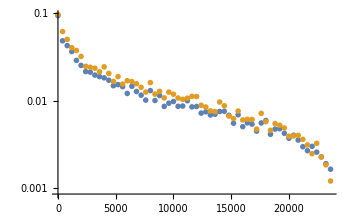

```mathematica
rmseRfplot = ListLogPlot[{rmseRfdata[[All,{1,3}]], rmseRfdata[[All,{1,4}]]}, PlotRange->All, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}]
```

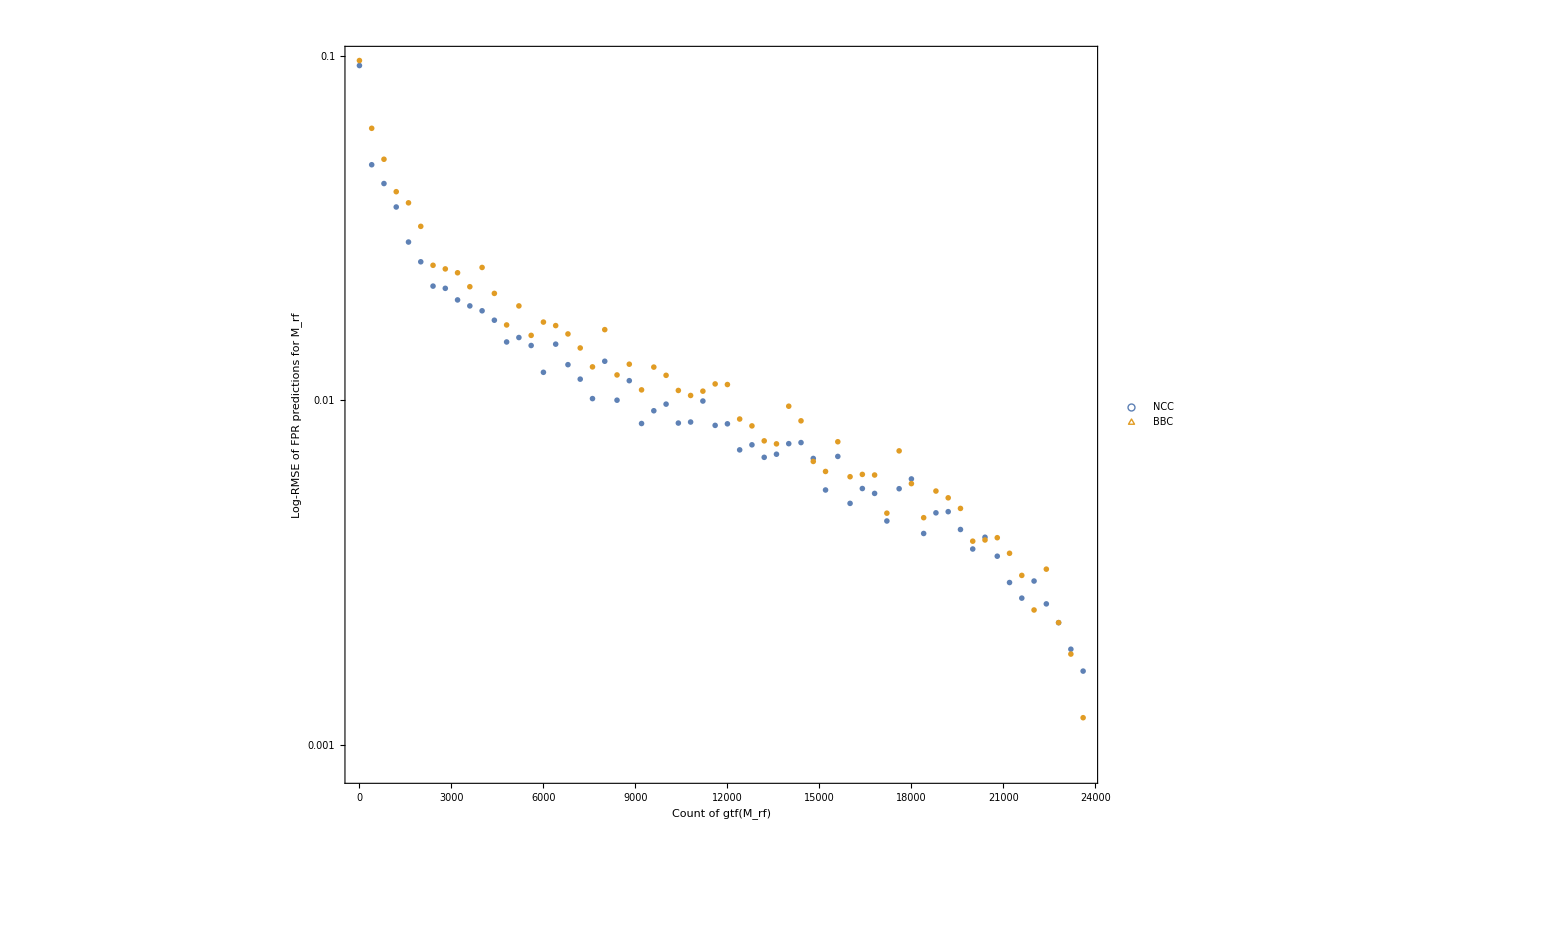

```mathematica
mseRfplotLegended = Legended[Show[rmseRfplot, Frame->True, FrameLabel->{StringJoin["Count of gtf", ToString[ Style[StringJoin["(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ], StringJoin["Log-RMSE of FPR predictions for ", ToString[Subscript[ "M", "rf"], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}],Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]} , {ColorData[97,"ColorList"][[2]]}},{"NCC", "BBC"},
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] , Style[△,Bold,FontSize->60] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.1,0.15}]]
```